barrier potential

```mathematica
Clear[a]
```

```mathematica
u[x_]:=d ⅇ^(-(-1/2+x)^2/(2 s^2))-(ⅇ^(-(-1-b+x)^2/(2 a^2))+ⅇ^(-(b+x)^2/(2 a^2))) k+1/2 w (2+Erf[r (-1-m+x)]-Erf[r (m+x)])
```

```mathematica
uph[x_]:=d ⅇ^(-(-1/2+x)^2/(2 s^2))-(ⅇ^(-(-1-b+x)^2/(2 a^2))+ⅇ^(-(b+x)^2/(2 a^2))) k+1/2 w (2+Erf[r (-1-m+x)]-Erf[r (m+x)])+x *sig^2*mass*Log[10]*(pka-ph)
```

```mathematica
params= {k->2.530,w->50,a->0.03371,b->0.004491,s->0.3,sigma0->0.02,r->21.428,d->2.0,m->0.1078,pka->4,ph->3};
(* for lambda particle *)
```

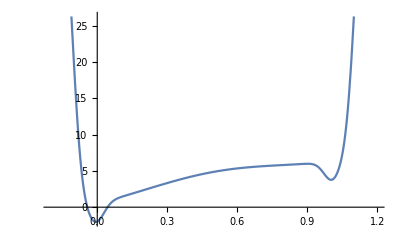

```mathematica
Plot[uph[x]/.params,{x,-0.2,1.2}]
```

```mathematica
params1= {k->2.530,w->50,a->0.03371,b->0.004491,s->0.3,sigma0->0.02,r->21.428,d->0.0,m->0.1078}; (* for buffer particle *)
```

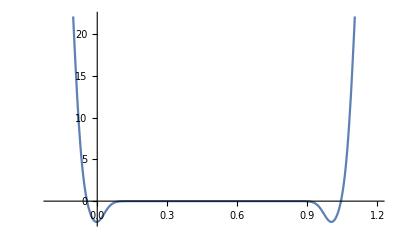

```mathematica
Plot[u[x]/.params1,{x,-0.2,1.2}]
```

derivative of the potential

```mathematica
g[x_]:=1/2 ((2 ⅇ^(-r^2 (-1-m+x)^2) r)/(√π)-(2 ⅇ^(-r^2 (m+x)^2) r)/(√π)) w-(d ⅇ^(-(-1/2+x)^2/(2 s^2)) (-1/2+x))/s^2-k (-(ⅇ^(-(-1-b+x)^2/(2 a^2)) (-1-b+x))/a^2-(ⅇ^(-(b+x)^2/(2 a^2)) (b+x))/a^2)
```

```mathematica
gph[x_]:=1/2 ((2 ⅇ^(-r^2 (-1-m+x)^2) r)/(√π)-(2 ⅇ^(-r^2 (m+x)^2) r)/(√π)) w-(d ⅇ^(-(-1/2+x)^2/(2 s^2)) (-1/2+x))/s^2-k (-(ⅇ^(-(-1-b+x)^2/(2 a^2)) (-1-b+x))/a^2-(ⅇ^(-(b+x)^2/(2 a^2)) (b+x))/a^2)+sig^2*mass*Log[10]*(pka-ph)
```

leap frog integrator

```mathematica
leapFrog[x_,v_,p_,step_,sig_]:=Module[{x1,v1},
v1=v+dt*(-g[x]/.p)/mass;
v1=andersen[step,v1,sig]; (* temperature coupling *)
x1=x+dt*v1;
Return[{x1,v1}];
]
```

```mathematica
leapFrogPh[x_,v_,p_,step_,sig_]:=Module[{x1,v1},
v1=v+dt*(-gph[x]/.p)/mass;
v1=andersen[step,v1,sig]; (* temperature coupling *)
x1=x+dt*v1;
Return[{x1,v1}];
]
```

andersen thermostat

```mathematica
andersen[step_,v_,sig_]:=Module[{},
If[Mod[step,tau] == 0,
Return[RandomVariate[NormalDistribution[0,sig],1][[1]]],
Return[v]];
];
```

initial parameters

```mathematica
tau=200;
dt=0.001;
mass=10;
```

```mathematica
(*integration parameters*)
(*integration parameters*)
nsteps=10000000;
dt=0.001;
tau=200;
sig=0.5;
(*initial conditions*)
For[i=1,i≤1,i++,
{
vold=RandomVariate[NormalDistribution[0,sig],1][[1]];
xold=0;
mass=10;
tol=10^-10;
constr=1;
(*Start 10 runs*)
(*trajectory*)
pos=ConstantArray[0,nsteps];
posb=ConstantArray[0,nsteps];
vel=ConstantArray[0,nsteps];
velb=ConstantArray[0,nsteps];
pos[[1]]=xold;
vel[[1]]=vold;
posb[[1]]=constr-pos[[1]];
velb[[1]]=-vold;
(*MD*)
For[t=2,t<=nsteps,t++,
{
(*md step*)
{pos[[t]],vel[[t]]}=leapFrogPh[pos[[t-1]],vel[[t-1]],params,t,sig];
{posb[[t]],velb[[t]]}=leapFrog[posb[[t-1]],velb[[t-1]],params1,t,sig];
};
];
DumpSave[dir<>"unconstr_poses_ph_sigma_0d5_"<>ToString[i]<>".mx",pos];
}
];
```

```mathematica
ListPlot[{pos+posb}]
```

-Graphics-

```mathematica
ListPlot[vel+velb]
```

-Graphics-

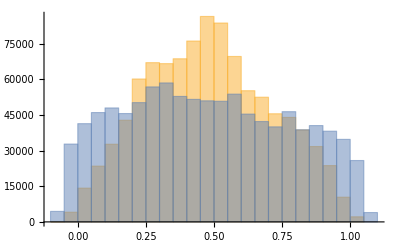

```mathematica
Histogram[{posb,posbC}]
```

constraints SHAKE

```mathematica
updatePosSHAKE[x1_,x2_,const_,tol_]:=Module[{x1O,x2O,x1N,x2N},
x1O=x1;
x2O=x2;
While[Abs[x1O+x2O-const]>tol,
x1N=x1O-(x1O+x2O-const)*0.5;
x2N=x2O-(x1O+x2O-const)*0.5;
x1O=x1N;
x2O=x2N;
];
Return[{x1O,x2O}];
]
```

```mathematica
leapFrogC[x1_,v1_,p1_,x2_,v2_,p2_,step_,sig_]:=Module[{x1n,v1n,x2n,v2n},
v1n=v1+dt*(-gph[x1]/.p1)/mass;
v2n=v2+dt*(-g[x2]/.p2)/mass;
v1n=andersen[step,v1n,sig]; (* temperature coupling *)
 v2n=If[Mod[step,tau] == 0,-v1n,v2n];
x1n=x1+dt*v1n;
x2n=x2+dt*v2n;
Return[{x1n,v1n,x2n,v2n}];
]
```

```mathematica
(*Start 10 runs*)
(*integration parameters*)
nsteps=10000000;
dt=0.001;
tau=200;
(*initial conditions*)
For[i=1,i≤1,i++,
{
vold=RandomVariate[NormalDistribution[0,sig],1][[1]];
xold=0;
mass=10;
tol=10^-10;
constr=1;
(*trajectory*)
posC=ConstantArray[0,nsteps];
posbC=ConstantArray[0,nsteps];
velC=ConstantArray[0,nsteps];
velbC=ConstantArray[0,nsteps];
posC[[1]]=xold;
velC[[1]]=vold;
posbC[[1]]=constr-posC[[1]];
velbC[[1]]=-vold;
(*MD*)
For[t=2,t<=nsteps,t++,
{
(*md step*)
{posC[[t]],velC[[t]],posbC[[t]],velbC[[t]]}=
leapFrogC[
posC[[t-1]],velC[[t-1]],params,
posbC[[t-1]],velbC[[t-1]],params1,
t,sig
];
(*constraints*)
{posC[[t]],posbC[[t]]}=updatePosSHAKE[posC[[t]],posbC[[t]],constr,tol];
(*velocity reconstruction*)
velC[[t]]=(posC[[t]]-posC[[t-1]])/dt;
velbC[[t]]=(posbC[[t]]-posbC[[t-1]])/dt;
If[Mod[t,10000]==0,a0=posC[[t]]+posbC[[t]]];
};
];
DumpSave[dir<>"constr_poses_ph_sigma_0d5_"<>ToString[i]<>".mx",posC];
}
];
```

```mathematica
Dynamic[t]
```

```mathematica
Dynamic[a0]
```

```mathematica
Dynamic[i]
```

compute energy profile from distribution

```mathematica
makeBinCounts[min_,max_,bins_,data_]:=Module[{interval,i},
interval=(max-min)/bins;
Return[
{Table[
(min+interval(i-0.5)),
{i,1,bins}],
BinCounts[data,{min,max,interval}]/(Length[data])}ᵀ];]
```

```mathematica
Get[dir<>"unconstr_poses_sigma_0d5_"<>ToString[i]<>".mx"]
```

```mathematica
countsU={};
For[i=1, i≤3,i++,
{
Get[dir<>"unconstr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
AppendTo[countsU,makeBinCounts[-0.2,1.2,280,pos]];
}
]
```

```mathematica
countsC={};
For[i=1, i≤3,i++,
{
Get[dir<>"constr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
AppendTo[countsC,makeBinCounts[-0.2,1.2,280,posC]];
}
]
```

```mathematica
xs=countsC[[1]]ᵀ[[1]];
```

```mathematica
prFromPot=Exp[-mass*sig^2*((u[#]/.params)&/@xs)];
prFromPot=prFromPot/Total[prFromPot];
```

```mathematica
prFromPotpH=Exp[-mass*sig^2*((uph[#]/.params)&/@xs)];
prFromPotpH=prFromPotpH/Total[prFromPotpH];
```

```mathematica
countsUpH=makeBinCounts[-0.2,1.2,280,pos];
```

```mathematica
countsCpH=makeBinCounts[-0.2,1.2,280,posC];
```

```mathematica
Max[prFromPot]
```

0.0772813

```mathematica
prFromPot[[140]]
```

3.52381×10^-6

```mathematica
Exp[-mass*sig^2*((u[0.5]-u[0])/.params)]*Max[prFromPot]
```

3.6724×10^-6

```mathematica
u[0]/.params
```

-1.98174

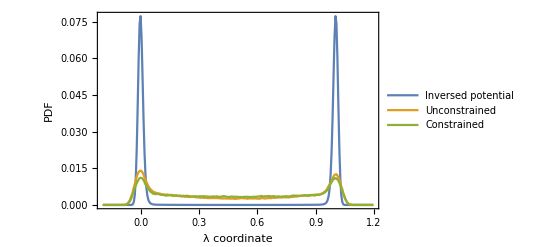

```mathematica
ListPlot[{
{xs,prFromPot}ᵀ,
countsU[[1]],
countsC[[1]]
},Joined->True,PlotRange->All,
PlotLegends->{"Inversed potential","Unconstrained","Constrained"},
Frame->True,
FrameLabel->{"λ coordinate", "PDF"}]
```

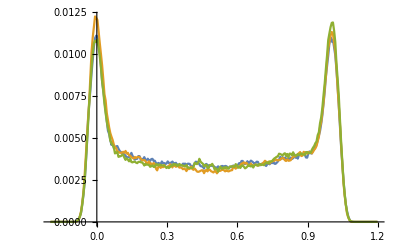

```mathematica
ListPlot[countsC,Joined->True]
```

```mathematica
pr=makeBinCounts[Min[pos],Max[pos],101,pos];
```

```mathematica
prᵀ[[2]]//Total
```

999999/1000000

```mathematica
dir=NotebookDirectory[];
```

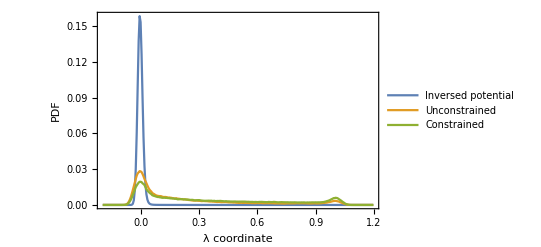

```mathematica
ListPlot[{
{xs,prFromPotpH}ᵀ,
countsUpH,
countsCpH
},Joined->True,PlotRange->All,
PlotLegends->{"Inversed potential","Unconstrained","Constrained"},
Frame->True,
FrameLabel->{"λ coordinate", "PDF"}]
```

titration run

```mathematica
(*Start 10 runs*)
(*integration parameters*)
nsteps=2000000;
dt=0.001;
tau=200;
posesCtit=ConstantArray[0,{17,nsteps}];
(*initial conditions*)
For[i=1,i≤17,i++,
{
params= {k->2.530,w->50,a->0.03371,b->0.004491,s->0.3,sigma0->0.02,r->21.428,d->2.0,m->0.1078,pka->4,ph->2+(i-1)*0.25};
(* for lambda particle *)
vold=RandomVariate[NormalDistribution[0,sig],1][[1]];
xold=0;
mass=10;
tol=10^-10;
constr=1;
(*trajectory*)
posCt=ConstantArray[0,nsteps];
posbCt=ConstantArray[0,nsteps];
velCt=ConstantArray[0,nsteps];
velbCt=ConstantArray[0,nsteps];
posCt[[1]]=xold;
velCt[[1]]=vold;
posbCt[[1]]=constr-posCt[[1]];
velbCt[[1]]=-vold;
(*MD*)
For[t=2,t<=nsteps,t++,
{
(*md step*)
{posCt[[t]],velCt[[t]],posbCt[[t]],velbCt[[t]]}=
leapFrogC[
posCt[[t-1]],velCt[[t-1]],params,
posbCt[[t-1]],velbCt[[t-1]],params1,
t,sig
];
(*constraints*)
{posCt[[t]],posbCt[[t]]}=updatePosSHAKE[posCt[[t]],posbCt[[t]],constr,tol];
(*velocity reconstruction*)
velCt[[t]]=(posCt[[t]]-posCt[[t-1]])/dt;
velbCt[[t]]=(posbCt[[t]]-posbCt[[t-1]])/dt;
If[Mod[t,10000]==0,a0=posCt[[t]]+posbCt[[t]]];
};
];
posesCtit[[i]]=posCt;
}
];
```

{1}
 |  |  |  |

```mathematica
DumpSave[dir<>"titC.mx",posesCtit];
```

```mathematica
nsteps0=10000000;
```

```mathematica
countsCp={};
For[j=1,j≤64,j*=2,
{
countsi={};
For[i=1, i≤3,i++,
{
Get[dir<>"constr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
pp=Partition[posC,nsteps0/j];
AppendTo[countsi,makeBinCounts[-0.2,1.2,280,#]&/@pp];
};
];
AppendTo[countsCp,countsi];
};
]
```

```mathematica
countsUp={};
For[j=1,j≤64,j*=2,
{
countsi={};
For[i=1, i≤3,i++,
{
Get[dir<>"unconstr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
pp=Partition[pos,nsteps0/j];
AppendTo[countsi,makeBinCounts[-0.2,1.2,280,#]&/@pp];
};
];
AppendTo[countsUp,countsi];
};
]
```

```mathematica
Flatten[countsCp[[2]],1]//Length
```

30

```mathematica
Flatten[countsCp[[2]],1]//Length
```

30

```mathematica
a123=Partition[posC,nsteps];
```

```mathematica
a123//Length
```

1

```mathematica
nsteps/64
```

156250

```mathematica
cmp2pdfs[c1_,c2_]:=Module[{cdf1,cdf2},
cdf1=Accumulate[c1ᵀ[[2]]]+0.;
cdf2=Accumulate[c2ᵀ[[2]]]+0.;
Return[Max[Abs[cdf1-cdf2]]];
];
```

```mathematica
stdOfPDFs[pdfL_]:=Module[{kssList},
kssList=Table[
cmp2pdfs[pdfL[[i[[1]]]],pdfL[[i[[2]]]]],
{i,Subsets[Range[Length[pdfL]],{2}]}];
Return[Mean[kssList]];
];
```

```mathematica
Table[{nsteps/2^(i-1),stdOfPDFs[Flatten[countsCp[[i]],1]]},{i,1,7,1}]
```

{{10000000,0.0206376},{5000000,0.0227018},{2500000,0.0365153},{1250000,0.0596302},{625000,0.0983872},{312500,0.135552},{156250,0.204491}}

```mathematica
cmp2pdfs[countsCp[[1,1,1]],countsCp[[7,3,1]]]
```

0.128791

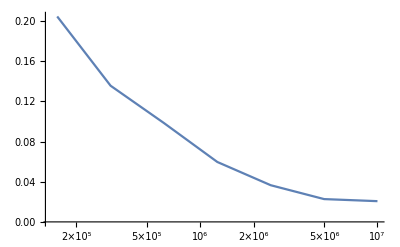

```mathematica
ListLogLinearPlot[Table[{nsteps/2^(i-1),stdOfPDFs[Flatten[countsCp[[i]],1]]},{i,1,7,1}],Joined->True,PlotRange->All]
```

```mathematica
simMean1[pos_]:=Module[{},
Return[Mean[pos]];
];
simMean2[pos_]:=Module[{},
Return[Mean[Select[pos,!(0.2<#<0.8)&]]];
];
```

```mathematica
simMean1[{0,0.3,1}]
```

0.433333

```mathematica
hh[x_]:=1/(10^(4-x)+1);
```

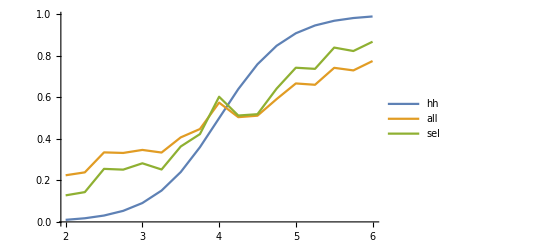

```mathematica
ListPlot[{
{#,hh[#]}&/@Range[2,6,0.25],
{Range[2,6,0.25],simMean1[#]&/@posesCtit}ᵀ,
{Range[2,6,0.25],simMean2[#]&/@posesCtit}ᵀ
},Joined->True,PlotLegends->{"hh","all","sel"}]
```

```mathematica
pos//Length
```

10000000

```mathematica
Select[pos,0.2<#<0.8&]//Length
```

3506191

```mathematica
Get[dir<>"unconstr_poses_sigma_0d5_"<>ToString[3]<>".mx"];
```

```mathematica
posC//Length
```

10000000

```mathematica
Select[posC,0.2<#<0.8&]//Length
```

3970526

```mathematica
uTr={};
cTr={};
```

```mathematica
For[i=1, i≤3,i++,
{
Get[dir<>"unconstr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
Get[dir<>"constr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
uplot=ListPlot[{Range[0,1000-0.001,0.001],pos[[;;1000000]]}ᵀ,
Frame->True,
Joined->True,
Axes->False,
FrameLabel->{"Time","λ"},
PlotLabel->"Unconstrained simulation "<>ToString[i]];
cplot=ListPlot[{Range[0,1000-0.001,0.001],posC[[;;1000000]]}ᵀ,
Frame->True,
Joined->True,
Axes->False,
FrameLabel->{"Time","λ"},
PlotLabel->"Constrained simulation "<>ToString[i]];
AppendTo[uTr,uplot];
AppendTo[cTr,cplot];
}
];
```

```mathematica
Export[dir<>"trajs.png",GraphicsGrid[{uTr,cTr},ImageSize->1200]]
```

/Users/pbuslaev/work/sim/200217_simple_md/trajs.png

```mathematica
upTr={};
cpTr={};
For[i=1, i≤7,i+=3,
upplot=ListPlot[Flatten[countsUp[[i]],1],
Joined->True,
Frame->True,
Axes->False,
FrameLabel->{"λ","PDF"},
PlotRange->All,
PlotLabel->"Unconstrained simulation, length  "<>ToString[10000000/2^(i-1)]];
cpplot=ListPlot[Flatten[countsCp[[i]],1],
Joined->True,
Frame->True,
Axes->False,
PlotRange->All,
FrameLabel->{"λ","PDF"},
PlotLabel->"Constrained simulation, length  "<>ToString[10000000/2^(i-1)]];
AppendTo[upTr,upplot];
AppendTo[cpTr,cpplot];
]
Export[dir<>"ptraj_distr.png",GraphicsGrid[{upTr,cpTr},ImageSize->1200]]
```

/Users/pbuslaev/work/sim/200217_simple_md/ptraj_distr.png

```mathematica
conv=ListLogLinearPlot[{
Table[{nsteps0/2^(i-1),stdOfPDFs[Flatten[countsUp[[i]],1]]},{i,1,7,1}],
Table[{nsteps0/2^(i-1),stdOfPDFs[Flatten[countsCp[[i]],1]]},{i,1,7,1}]},
Joined->True,
FrameTicks->{
{{0,0.05,0.1,0.15,0.2},None},
{{nsteps0/64,nsteps0/32,nsteps0/16,nsteps0/8,nsteps0/4,nsteps0/2,nsteps0},None}
},
FrameLabel->{"Length","KSS"},
PlotLegends->{"Unconstrained","Constrained"},
Frame->True,
PlotRange->All,ImageSize->600];
```

```mathematica
Export[dir<>"convergence.png",conv]
```

/Users/pbuslaev/work/sim/200217_simple_md/convergence.png

```mathematica
eqDistr=ListPlot[{
{xs,prFromPot}ᵀ,
countsU[[1]],
countsU[[2]],
countsU[[3]],
countsC[[1]],
countsC[[2]],
countsC[[3]]
},
Joined->True,
Frame->True,
PlotLabel->"pH=pKa=4",
FrameLabel->{"λ","PDF"},
PlotRange->All,
PlotStyle->{Black,Red,Darker[Red],Lighter[Red],Green,Darker[Green],Lighter[Green]},
PlotLegends->Placed[{
"Inversed potential",
"Unconstrained 1",
"Unconstrained 2",
"Unconstrained 3",
"Constrained 1",
"Constrained 2",
"Constrained 3"},{Center,Center}],ImageSize->600];
neqDistr=ListPlot[{
{xs,prFromPotpH}ᵀ,
countsUpH,
countsCpH
},
Joined->True,
Frame->True,
PlotLabel->"pH=3; pKa=4",
FrameLabel->{"λ","PDF"},
PlotRange->All,
PlotStyle->{Black,Red,Green},
PlotLegends->Placed[{
"Inversed potential",
"Unconstrained",
"Constrained"},{Center,Center}],ImageSize->600];
Export[dir<>"compToInv.png",GraphicsGrid[{{eqDistr,neqDistr}},ImageSize->1200]]
```

/Users/pbuslaev/work/sim/200217_simple_md/compToInv.png

```mathematica
eqDistr1=ListPlot[{
countsU[[1]],
countsU[[2]],
countsU[[3]],
countsC[[1]],
countsC[[2]],
countsC[[3]]
},
Joined->True,
Frame->True,
PlotLabel->"pH=pKa=4",
FrameLabel->{"λ","PDF"},
PlotRange->All,
PlotStyle->{Red,Darker[Red],Lighter[Red],Green,Darker[Green],Lighter[Green]},
PlotLegends->Placed[{
"Unconstrained 1",
"Unconstrained 2",
"Unconstrained 3",
"Constrained 1",
"Constrained 2",
"Constrained 3"},{Center,Center}],ImageSize->600];
neqDistr1=ListPlot[{
countsUpH,
countsCpH
},
Joined->True,
Frame->True,
PlotLabel->"pH=3; pKa=4",
FrameLabel->{"λ","PDF"},
PlotRange->All,
PlotStyle->{Red,Green},
PlotLegends->Placed[{
"Unconstrained",
"Constrained"},{Center,Center}],ImageSize->600];
Export[dir<>"effect_of_shake.png",GraphicsGrid[{{eqDistr1,neqDistr1}},ImageSize->1200]]
```

/Users/pbuslaev/work/sim/200217_simple_md/effect_of_shake.png

```mathematica
For[i=1,i≤3,i++,
Get[dir<>"unconstr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
Get[dir<>"constr_poses_sigma_0d5_"<>ToString[i]<>".mx"];
Print[Select[pos,0.2<#<0.8&]//Length];
Print[Select[posC,0.2<#<0.8&]//Length];
]
```

3480487

4166880

3614460

3970526

3506191

4080175

```mathematica
Get[dir<>"unconstr_poses_ph_sigma_0d5_"<>ToString[1]<>".mx"];
Get[dir<>"constr_poses_ph_sigma_0d5_"<>ToString[1]<>".mx"];
Print[Select[pos,0.2<#<0.8&]//Length];
Print[Select[posC,0.2<#<0.8&]//Length];
```

2743482

3642672

```mathematica
3480487/10000000.
```

0.348049

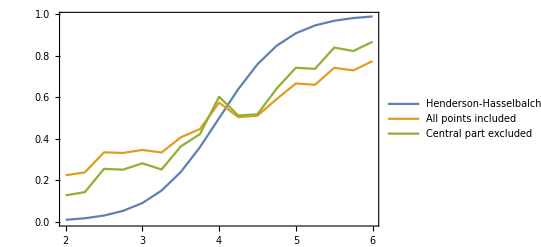

```mathematica
ListPlot[{
{#,hh[#]}&/@Range[2,6,0.25],
{Range[2,6,0.25],simMean1[#]&/@posesCtit}ᵀ,
{Range[2,6,0.25],simMean2[#]&/@posesCtit}ᵀ
},
Frame->True,
Joined->True,
PlotLegends->{"Henderson-Hasselbalch","All points included","Central part excluded"}]
```